```mathematica
f[x_]:=(1-(x^2-xmu2)/((x x-xmu2)^2+xdt2)^(1/2))x x
```

```mathematica
f[x]
```

x^2 (1-(x^2-xmu2)/(√(xdt2+(x^2-xmu2)^2)))

```mathematica
NIntegrate[f[x]/.{xmu2->1,xdt2->0.0001},{x,0,Infinity}]
```

0.666846

```mathematica
N[%]
```

0.666846

```mathematica
NSolve[NIntegrate[(f[x]/.{xmu2->0.9}),{x,0,Infinity}]==2/3,{xdt2},Reals]
```

NIntegrate::inumr: The integrand x^2\ (1 - -0.9 + x^2/√(-0.9 + Power[« 2 »])^2 + xdt2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{}

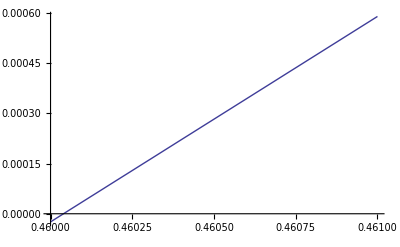

```mathematica
Plot[NIntegrate[(f[x]/.{xmu2->0.6}),{x,0,Infinity}]-2/3,{xdt2,0.46,0.461}]
```

```mathematica
N[8Pi^3/3]
```

82.6834

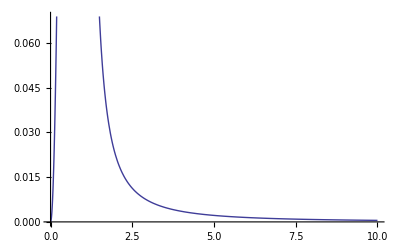

```mathematica
Plot[f[x]/.{xmu2->0.99,xdt2->0.1},{x,0,10}]
```

```mathematica
muDtL={{0.999,0.00064},{0.99,0.0079665},{0.95,0.059435},{0.93,0.0693},{0.9,0.10298},{0.7,0.34},{0.6,0.46005},{0.5,.577},{.3,.8005},{.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-.5,1.545},{-.7,1.7},{-.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.4}}
```

{{0.999,0.00064},{0.99,0.0079665},{0.95,0.059435},{0.93,0.0693},{0.9,0.10298},{0.7,0.34},{0.6,0.46005},{0.5,0.577},{0.3,0.8005},{0.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-0.5,1.545},{-0.7,1.7},{-0.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.4}}

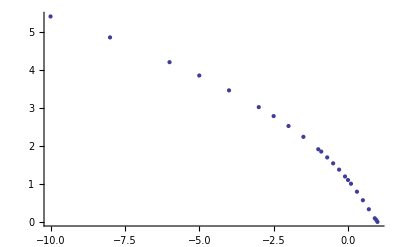

```mathematica
ListPlot[muDtL]
```

```mathematica
f1[x_]:=(x x)/((x x-xmu2)^2+xdt4)^(1/2)-1
```

```mathematica
f1[x]
```

-1+x^2/(√(xdt4+(x^2-xmu2)^2))

```mathematica
f1[x]mu{xmu2->1,xdt4->2}
```

{mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xmu2→1),mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xdt4→2)}

```mathematica
length=Length[muDtL];intact={};
For[i=1,i≤length,i++,
strength=2/Pi NIntegrate[f1[x]/.{xmu2->muDtL[[i,1]],xdt4->muDtL[[i,2]]},{x,0,Infinity}];intact=Append[intact,strength]]
```

```mathematica
intact
```

{2.38973,1.5756,0.899421,0.830708,0.680721,0.166638,0.0128024,-0.113235,-0.316811,-0.481182,-0.553235,-0.620286,-0.742788,-0.852479,-0.952547,-1.04524,-1.08865,-1.28824,-1.46346,-1.6213,-1.76587,-2.02578,-2.25686,-2.46689,-2.84159,-3.17282}

```mathematica
muL=Transpose[muDtL][[1]];dtL=Transpose[muDtL][[2]]^(1/2);
```

```mathematica
muL
```

{0.99,0.9,0.7,0.5,0.3,0.1,0,-0.1,-0.3,-0.5,-0.7,-0.9,-1,-1.5,-2,-2.5,-3,-4,-5,-6,-8,-10}

```mathematica
Transpose[{intact,muL}]
```

{{2.38973,0.999},{1.5756,0.99},{0.899421,0.95},{0.830708,0.93},{0.680721,0.9},{0.166638,0.7},{0.0128024,0.6},{-0.113235,0.5},{-0.316811,0.3},{-0.481182,0.1},{-0.553235,0},{-0.620286,-0.1},{-0.742788,-0.3},{-0.852479,-0.5},{-0.952547,-0.7},{-1.04524,-0.9},{-1.08865,-1},{-1.28824,-1.5},{-1.46346,-2},{-1.6213,-2.5},{-1.76587,-3},{-2.02578,-4},{-2.25686,-5},{-2.46689,-6},{-2.84159,-8},{-3.17282,-10}}

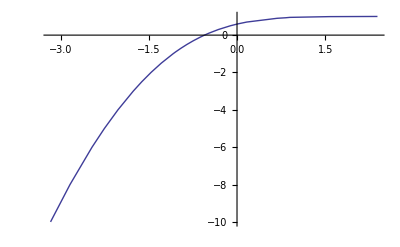

```mathematica
muPlot=ListLinePlot[Transpose[{intact, muL}]]
```

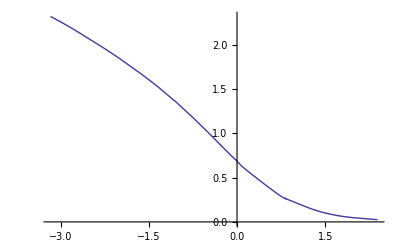

```mathematica
dtPlot=ListLinePlot[Transpose[{intact,dtL}],InterpolationOrder->2]
```

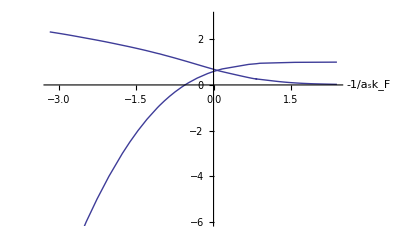

```mathematica
Show[dtPlot,muPlot,AxesLabel->{"-1/a_sk_F",""},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

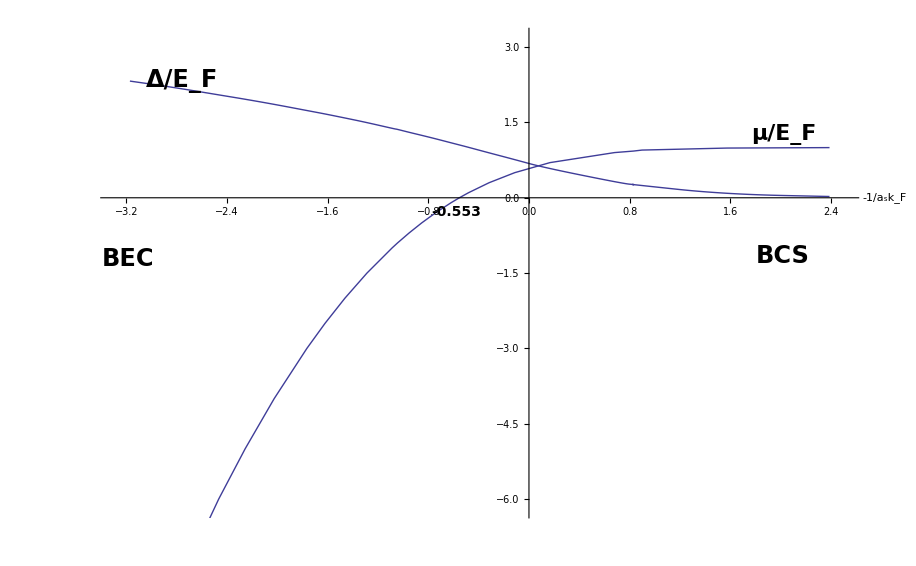

```mathematica
shiftIntact=intact*10+muL*2
```

{25.8953,17.736,10.8942,10.1671,8.60721,3.06638,1.32802,-0.13235,-2.56811,-4.61182,-5.53235,-6.40286,-8.02788,-9.52479,-10.9255,-12.2524,-12.8865,-15.8824,-18.6346,-21.213,-23.6587,-28.2578,-32.5686,-36.6689,-44.4159,-51.7282}

```mathematica
intactSt2=intact*5+muL*2
```

{13.9466,9.858,6.3971,6.01354,5.20361,2.23319,1.26401,0.433825,-0.984054,-2.20591,-2.76618,-3.30143,-4.31394,-5.26239,-6.16273,-7.02621,-7.44323,-9.44121,-11.3173,-13.1065,-14.8294,-18.1289,-21.2843,-24.3344,-30.208,-35.8641}

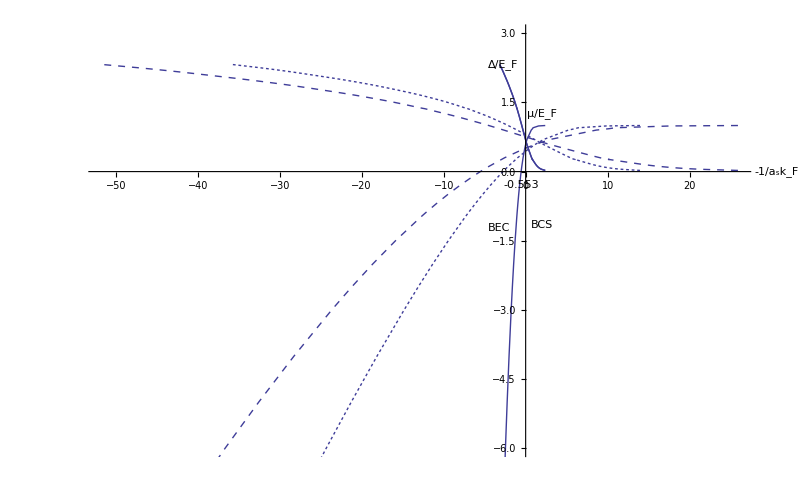

```mathematica
muPlotSt=ListLinePlot[Transpose[{shiftIntact, muL}],PlotStyle->{Dashed}];dtPlotSt=ListLinePlot[Transpose[{shiftIntact,dtL}],InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactSt2, muL}],PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactSt2,dtL}],InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,muPlot,muPlotSt2,dtPlotSt2,s,AxesLabel->{"-1/a_sk_F",""},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

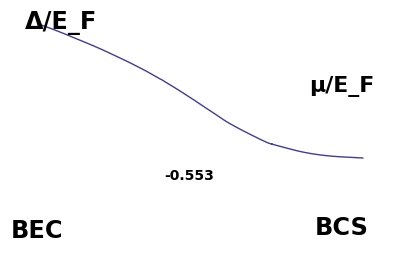
```mathematica
s=-Graphics-
```

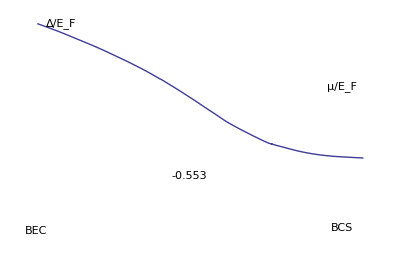

```mathematica
muDtL[[1]]
```

{0.99,0.008}

```mathematica
Length[muDtL]
```

26

```mathematica
a=0;a=
```